## AIM: To Solve a problem in probability using Bayes Rule by both Theoretically and using Monte Carlo method.

```mathematica
(*Question A*)
μ1=90;(*True IQ of A*)
μ2=110;(*True IQ of B*)
c=N[1/(2 Pi)^0.5,200];
pdf1[x_,σ_]:=c/σ ⅇ^((-(x-μ1)^2)/(2 σ^2))
pdf2[x_,σ_]:=c/σ ⅇ^((-(x-μ2)^2)/(2 σ^2))

pA=0.5;
pB=0.5;
pyA = pdf1[105,t];
pyB = pdf2[105,t];  

totp=pyA*pA+pyB*pB;
pAy = (pyA*pA)/totp//Simplify
pBy = (pyB*pB)/totp//Simplify
(*To find the second recording, we have to take the weighted average of the IQ value *)

sndrcd1=Limit[90*pAy+110*pBy,t->3]
```

1./(1.+1. ⅇ^(100/t^2))

(1. ⅇ^(100/t^2))/(1.+1. ⅇ^(100/t^2))

110.

```mathematica
(*Question B
t->20*)

sndrcd2=Limit[90*pAy+110*pBy,t->20]
```

101.244

```mathematica
(*Extra:This is the case where the standard deviation tends to 0 or infinity. For the case t->0, the graph will be a function which is zero everywhere except when it is peak value which is infinity.Therefore,if the first recording is close to whichever spike the second recording will be that peak's IQ value. For the case t->Infinity, all the values equiprobable therefore pAy = pBy = 1/2 and that's why *)
sndrcd0=Limit[90*pAy+110*pBy,t->0]
sndrcdinf=Limit[90*pAy+110*pBy,t->Infinity]
```

110.

100.

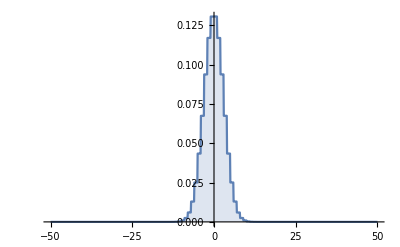

```mathematica
dist1=RandomVariate[NormalDistribution[0,3],100000000];
dist2=RandomVariate[NormalDistribution[20,3],100000000];
hist1=HistogramDistribution[dist1];
hist2=HistogramDistribution[dist2];
DiscretePlot[PDF[hist1,x],{x,-50,50,0.1},PlotRange->All]
PDF[hist1,x]
PDF[hist2,x]
```

```mathematica
(*From Monte Carlo method*)
pyAE1=2*10^-7;
pyBE1=0.04343474;
(*Then Using the formula to find the second recording of the IQ when the first recording is 105.*)
secrndE1 = 90*(pyAE1/(pyAE1+pyBE1))+110*(pyBE1/(pyAE1+pyBE1))
```

110.

```mathematica
dist3=RandomVariate[NormalDistribution[0,20],100000000];
dist4=RandomVariate[NormalDistribution[20,20],100000000];
hist3=HistogramDistribution[dist3];
hist4=HistogramDistribution[dist4];
DiscretePlot[PDF[hist3,x],{x,-500,500,0.01},PlotRange->All]
PDF[hist3,x];
PDF[hist4,x];
```

-Graphics-

```mathematica
(*From Monte Carlo method*)
pyAE2=0.014990855;
pyBE2=0.019140279;
(*Then Using the formula to find the second recording of the IQ when the first recording is 105.*)
secrndE2 = 90*(pyAE2/(pyAE2+pyBE2))+110*(pyBE2/(pyAE2+pyBE2))
```

101.216